```mathematica
(* flux balance for Subscript[C, org] with only photosynthesis and CO2 fixation *)
(*fluxRelations ={Subscript[J, cat]->Subscript[v, cat]*Subscript[C, nt]*Subscript[ϕ, cat]*Subscript[C, prot],
Subscript[J, ana]->Subscript[v, ana]*Subscript[C, int]*Subscript[ϕ, ana]*Subscript[C, prot],
Subscript[J, ferm]->Subscript[v, ferm]*Subscript[C, int]*Subscript[ϕ, ferm]*Subscript[C, prot]};
Subscript[dC, int]=2 Subscript[J, cat]-Subscript[J, ana]-Subscript[J, ferm]/.fluxRelations
Subscript[dC, ECH]=4 Subscript[J, cat]-750 Subscript[J, ana]-4 Subscript[J, ferm]/.fluxRelations
Subscript[dC, ATP]=2 Subscript[J, cat]-1500 Subscript[J, ana]-Subscript[v, O]*Subscript[ϕ, O]*Subscript[C, prot]/.fluxRelations
*)
μ[Subscript[ϕ, ana]_, Subscript[S, 2]_]= (-1/Subscript[S, b]+ √(1/Subscript[S, b]^2+4((Subscript[S, 8] Subscript[K, 1])/(Subscript[K, 2] N^(Subscript[S, 2]-Subscript[S, 6]) Subscript[ϕ, ana]))(1-Subscript[ϕ, o]-Subscript[ϕ, ana])))/(2/(Subscript[K, 2] N^Subscript[S, 2] Subscript[ϕ, ana]));
Solve[{D[μ[Subscript[ϕ, ana]], Subscript[ϕ, ana]] == 0}, {Subscript[ϕ, ana]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ_ana→InverseFunction[μ',1,1][0]}}

```mathematica
Subscript[ϕ, ana]/.{{Subscript[ϕ, ana]->InverseFunction[μ',1,1][0]}}
```

{InverseFunction[μ',1,1][0]}

```mathematica
First[{{Subscript[ϕ, ana]->InverseFunction[μ',1,1][0]}}]
```

{ϕ_ana→InverseFunction[μ',1,1][0]}

```mathematica
Subscript[S, b]=1; 
Subscript[S, 8]=1;
Subscript[K, 1]=1;
Subscript[K, 2]=1;
Subscript[S, 6]=1;
Subscript[ϕ, o]=0.01;
A = 2.2;
μ=(-1/Subscript[S, b]+ √(1/Subscript[S, b]^2+4((Subscript[S, 8] Subscript[K, 1])/(Subscript[K, 2] A^(Subscript[S, 2]-Subscript[S, 6]) Subscript[ϕ, ana]))(1-Subscript[ϕ, o]-Subscript[ϕ, ana])))/(2/(Subscript[K, 2] A^Subscript[S, 2] Subscript[ϕ, ana]));
Plot3D[μ, {Subscript[ϕ, ana], 0, 1}, {Subscript[S, 2], 0, 5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Subscript[K, 1]=1;
Subscript[K, 2]=1;
Subscript[K, 3]=1;
Subscript[ϕ, o]=0.1;
Subscript[ϕ, ana]=0.1;
ContourPlot3D[μ^(1-1/Subscript[S, 6])+Subscript[K, 3]*Subscript[S, 6]*μ^(1-2/Subscript[S, 6])==(2((Subscript[K, 1]+Subscript[K, 2])Subscript[ϕ, cat]-Subscript[K, 2](1-Subscript[ϕ, o]-Subscript[ϕ, ana])))/(Subscript[K, 3] Subscript[ϕ, ana]^(1/Subscript[S, 6])),{μ, 0.01, 10}, {Subscript[S, 6], 0.1, 3},{Subscript[ϕ, cat], 0.1, 0.99}, AxesLabel->Automatic]
```

-Graphics3D-

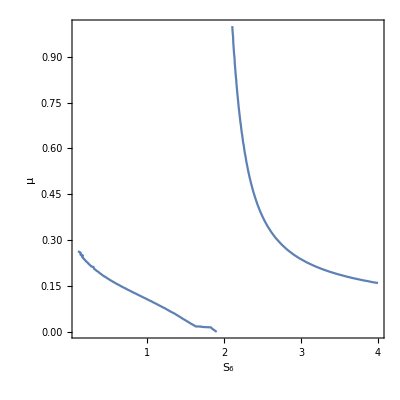

```mathematica
Subscript[K, 1]=1.2;
Subscript[K, 2]=1;
Subscript[K, 3]=1;
Subscript[ϕ, o]=0.1;
Subscript[ϕ, ana]=0.1;
Subscript[ϕ, cat]=0.6;
ContourPlot[μ^(1-1/Subscript[S, 6])+Subscript[K, 3]*Subscript[S, 6]*μ^(1-2/Subscript[S, 6])==(2((Subscript[K, 1]+Subscript[K, 2])Subscript[ϕ, cat]-Subscript[K, 2](1-Subscript[ϕ, o]-Subscript[ϕ, ana])))/(Subscript[K, 3] Subscript[ϕ, ana]^(1/Subscript[S, 6])), {Subscript[S, 6], 0.1, 4}, {μ, 0.0, 1},AxesLabel->Automatic]
```

```mathematica
Subscript[S, 4]=1; 
Subscript[S, 3]=1;
Subscript[K, 1]=.1;
Subscript[K, 2]=.1;
Subscript[K, 3]=.1;
Subscript[K, 4]=.1;
Subscript[ϕ, o]=0.01;
Subscript[ϕ, cat]=0.5;
A=1.2;
μ=(Subscript[S, 4] Subscript[K, 2] Subscript[K, 4] Subscript[ϕ, ana](1-Subscript[ϕ, o]-Subscript[ϕ, ana]-Subscript[ϕ, cat])A^(Subscript[S, 6]+2))/(Subscript[S, 3] Subscript[K, 1] Subscript[ϕ, cat]-Subscript[K, 2] Subscript[K, 3] Subscript[ϕ, ana] A^Subscript[S, 6]);
Plot3D[μ, {Subscript[ϕ, ana], 0, .5}, {Subscript[S, 6], 1, 5},AxesLabel->Automatic, PlotRange->{0, Full}]
```

-Graphics3D-